```mathematica
PathGr[n_]:=Graph[Range[n],Table[k<->k+1,{k,n-1}]]
```

```mathematica
CycleGr[l_List]:=Graph[l,Append[Table[l[[k]]<->l[[k+1]],{k,Length[l]-1}],l[[1]]<->l[[Length[l]]]],VertexLabels->"Name"]
```

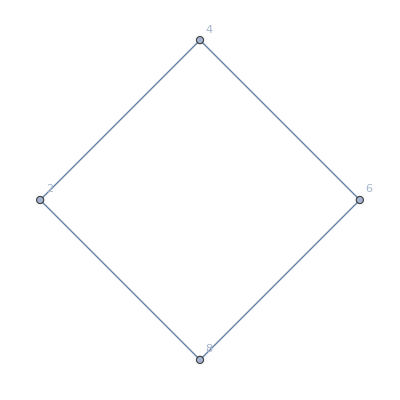

```mathematica
CycleGr[{2,4,6,8}]
```

```mathematica
sydGuessHeight2[txt_,w_: 100]:=Graphics[{Inset[Framed@TextCell[Style[txt,LineIndent->0,TextAlignment->Left],"Text",CellMargins->{{200,200},{10,10}}],{0,0},{0,0},{w,StringLength[txt]*(100*50)/(460*w)}]},PlotLabel->Style["syd guess: w="<>ToString[w],Red,Bold]]

txt2=(StringJoin@@Table["The quick brown fox jumped over the lazy dog. ",{20}]);
sydGuessHeight2[txt2,50]
```

-Graphics-

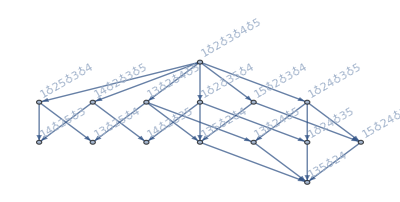

```mathematica
FindFullFormula[PathGr[5]]//FormulaGraphReverse2
```

EdgeList::argt: EdgeList called with 0 arguments; 1 or 2 arguments are expected.

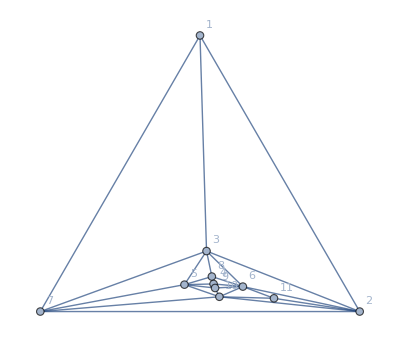

```mathematica
g=Graph[ReadGrof[900],VertexLabels->"Name",GraphLayout->"TutteEmbedding", GraphHighlight->CollectMPGEdges[g]]
```

```mathematica
ApplyToGraph[g_Graph,sets_List]:=Block[{result=g, vertexLabels=Association[]},
Table[
vertexLabels[bucket[[1]]]=Column[bucket];
If[Length[bucket]≠1,
result=VertexContract[result,bucket];
vertexLabels[bucket[[1]]]=Framed[Column[bucket,Alignment->Center]];
],
{bucket,sets}
];
Graph[result, VertexLabels->Normal[vertexLabels]]
]
```

```mathematica
ApplyToGraph2[g_Graph,sets_List]:=With[{h=ApplyToGraph[g,sets]},
Labeled[g,ChromaticPolynomial[h,x]]
]
```

```mathematica
MakeComplete[g_,vertices_]:=Block[{result=g},
Table[
If[!EdgeQ[result,fromto],
result=EdgeAdd[result,fromto]
],
{fromto,Map[#[[1]]<->#[[2]]&,Subsets[vertices,{2}]]}
];
Graph[VertexList[result],EdgeList[result],VertexLabels->"Name"]
]
```

```mathematica
GraphWithChrom[g_]:=Block[{chrom=ChromaticPolynomial[g,x],chrom4},
chrom4=chrom/.x->4;
Labeled[g,Style[{Factor[chrom/(x(x-1))],chrom4,PlanarGraphQ[g]},If[chrom4!=0,Darker[Green],Red],If[PlanarGraphQ[g],Underlined,Bold],8]]
]
```

```mathematica
TextCell
```

TextCell

```mathematica
SolToSymbol[sol_,vertices_]:=Block[{sets,sol2},
sol2=If[ListQ[sol],sol,SymbolToSets[sol]];
sets=Table[
Table[First[FirstPosition[vertices,b]],{b,bucket}]
,{bucket,sol2}
];
SetsToSymbol[Sort[Map[Sort,sets],#1[[1]]<#2[[1]]&]]
]
```

```mathematica
SolToSymbol[v3ax56,{3,6,10,5}]
```

v13x24

```mathematica
WorkOnGraph[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Column[
{GraphWithChrom[Graph[EdgeList[g],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{SolToSymbol[sol,vertices]/.RepGraph["C"],GraphWithChrom[lefta],GraphWithChrom[righta],GraphWithChrom[middlea]},
{sol,sols}
]
]
}
]
]
```

```mathematica
VertexCount[plantri8]
```

17

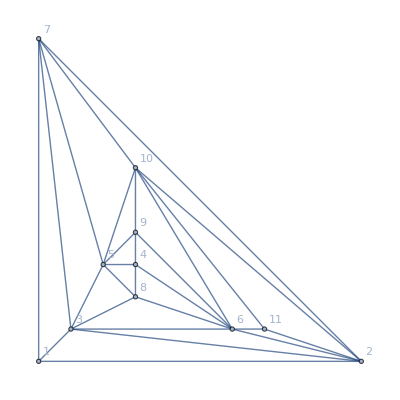
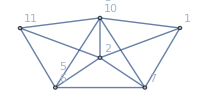
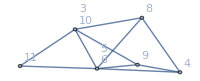
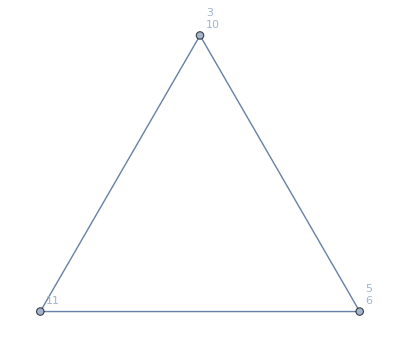
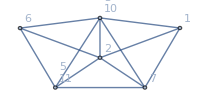
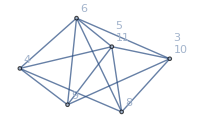
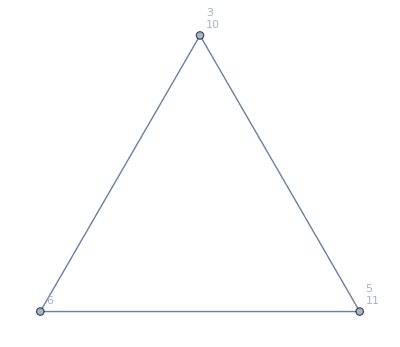
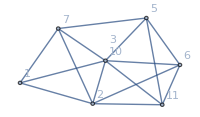
-Graphics-{(-3+x)^3 (-2+x) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),216,True}
-Graphics-317380 | -Graphics-{(-3+x)^3 (-2+x),24,True} | -Graphics-{(-2+x)^2 (7-5 x+x^2),144,True} | -Graphics-{-2+x,24,True}
-Graphics-317140 | -Graphics-{(-3+x)^3 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (13-7 x+x^2),24,False} | -Graphics-{-2+x,24,True}
-Graphics-317110 | -Graphics-{(-3+x)^2 (-2+x) (10-6 x+x^2),48,False} | -Graphics-{(-3+x)^2 (-2+x) (13-7 x+x^2),24,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-361120 | -Graphics-{(-4+x) (-3+x)^2 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (5-4 x+x^2),120,True} | -Graphics-{-2+x,24,True}
-Graphics-360850 | -Graphics-{(-3+x)^2 (-2+x) (13-7 x+x^2),24,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (10-6 x+x^2),0,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295510 | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0,False} | -Graphics-{(-3+x)^2 (-2+x) (5-4 x+x^2),120,True} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295270 | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (10-6 x+x^2),0,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295240 | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (17-8 x+x^2),0,False} | -Graphics-{(-4+x)^2 (-3+x) (-2+x) (10-6 x+x^2),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}

```mathematica
WorkOnGraph[g,{3,6,11,10,5}]
```

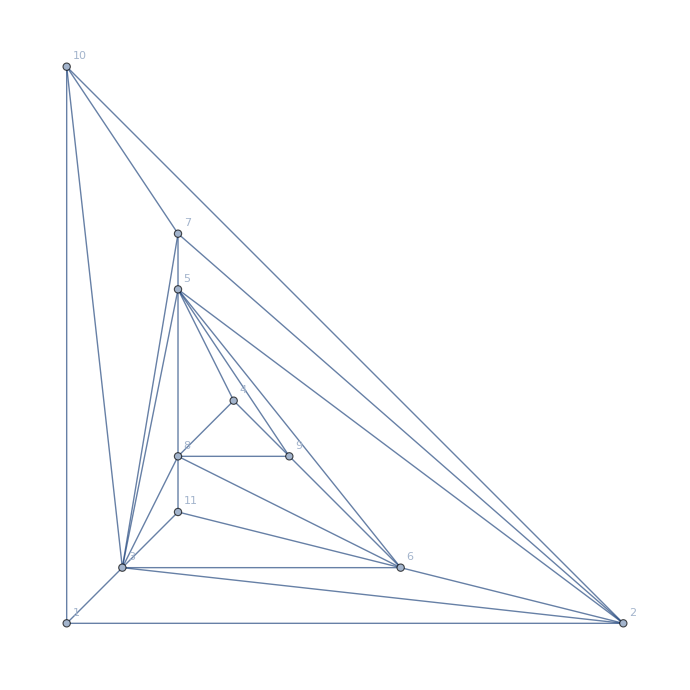

```mathematica
Graph[ReadGrof[1000],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

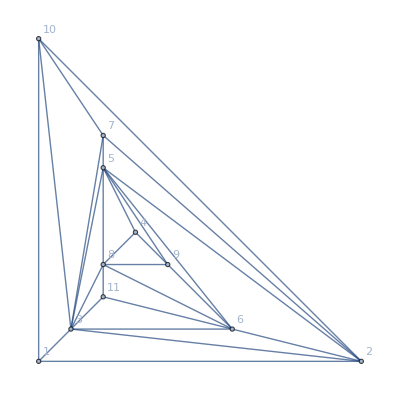
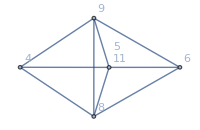
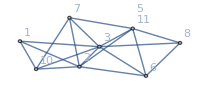
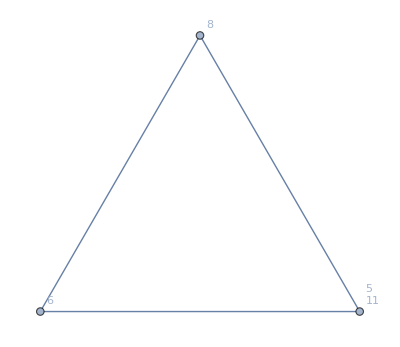
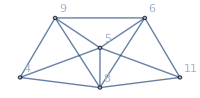
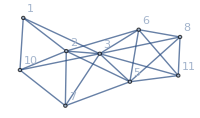
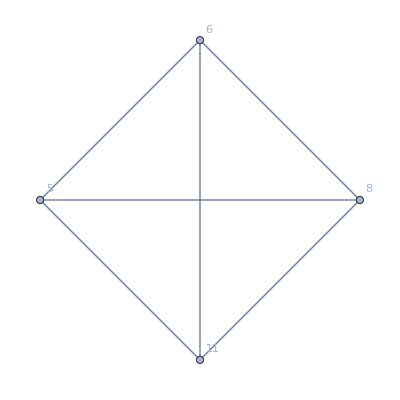
-Graphics-{(-3+x)^8 (-2+x),24,True}
v13x2x4 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-3+x)^5 (-2+x),24,True} | -Graphics-{-2+x,24,True}
v1x2x3x4 | -Graphics-{(-3+x)^3 (-2+x),24,True} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0,False} | -Graphics-{(-3+x) (-2+x),24,True}

```mathematica
ex2=WorkOnGraph[ReadGrof[1000],{5,6,11,8}]
```

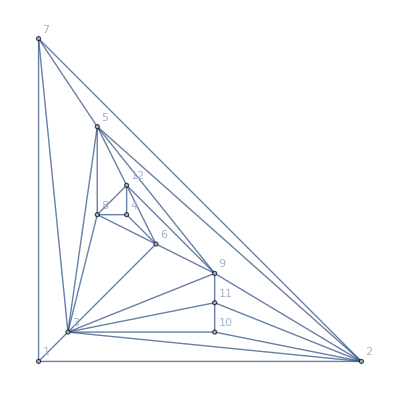

```mathematica
Graph[ReadGrof[5000],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

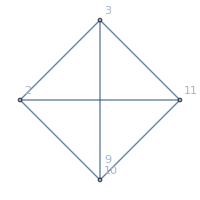
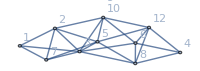
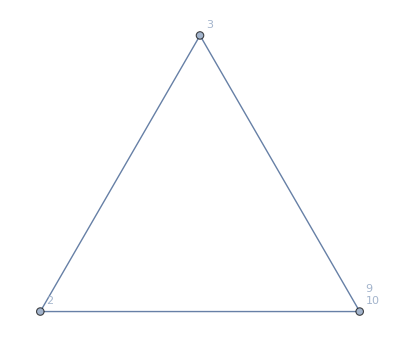
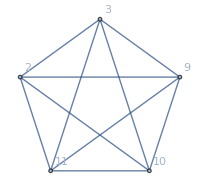
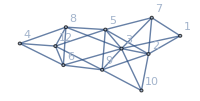
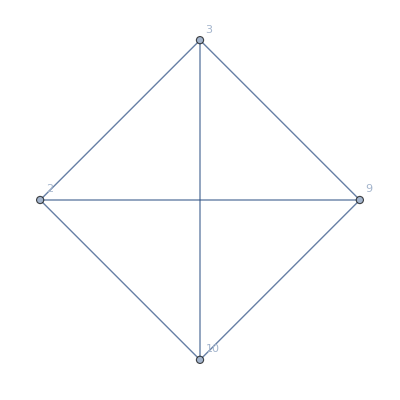
-Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96,True}
v1x24x3 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^4 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{-2+x,24,True}
v1x2x3x4 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x)^5 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{(-3+x) (-2+x),24,True}

```mathematica
WorkOnGraph[ReadGrof[5000],{2,10,3,9}]
```

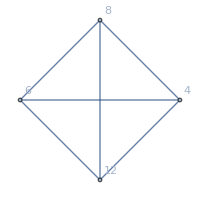
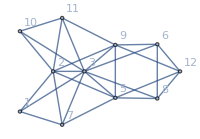
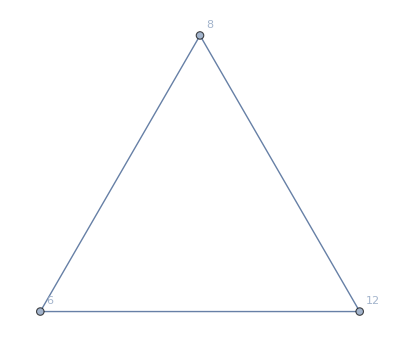
-Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96,True}
v1x2x3 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^5 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{-2+x,24,True}

```mathematica
WorkOnGraph[ReadGrof[5000],{12,6,8}]
```

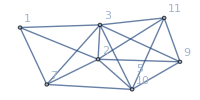
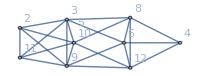
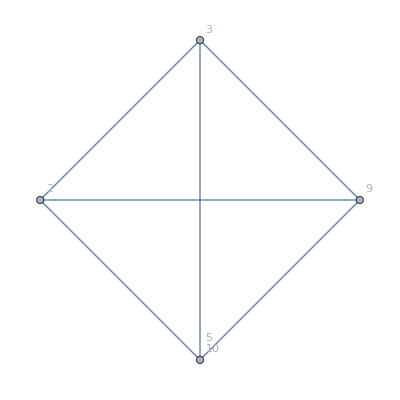
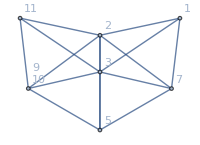
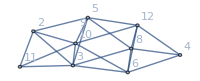
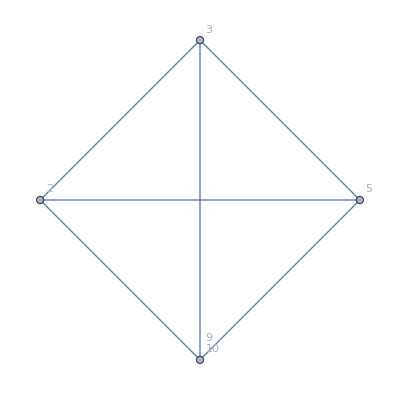
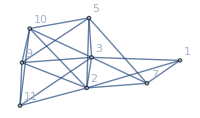
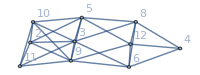
-Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96,True}
-Graphics-317110 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0,False} | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-296050 | -Graphics-{(-3+x)^4 (-2+x),24,True} | -Graphics-{(-3+x)^3 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295240 | -Graphics-{(-4+x)^2 (-3+x)^3 (-2+x),0,False} | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}

```mathematica
ex2=WorkOnGraph[ReadGrof[5000],{5,9,2,10,3}]
```

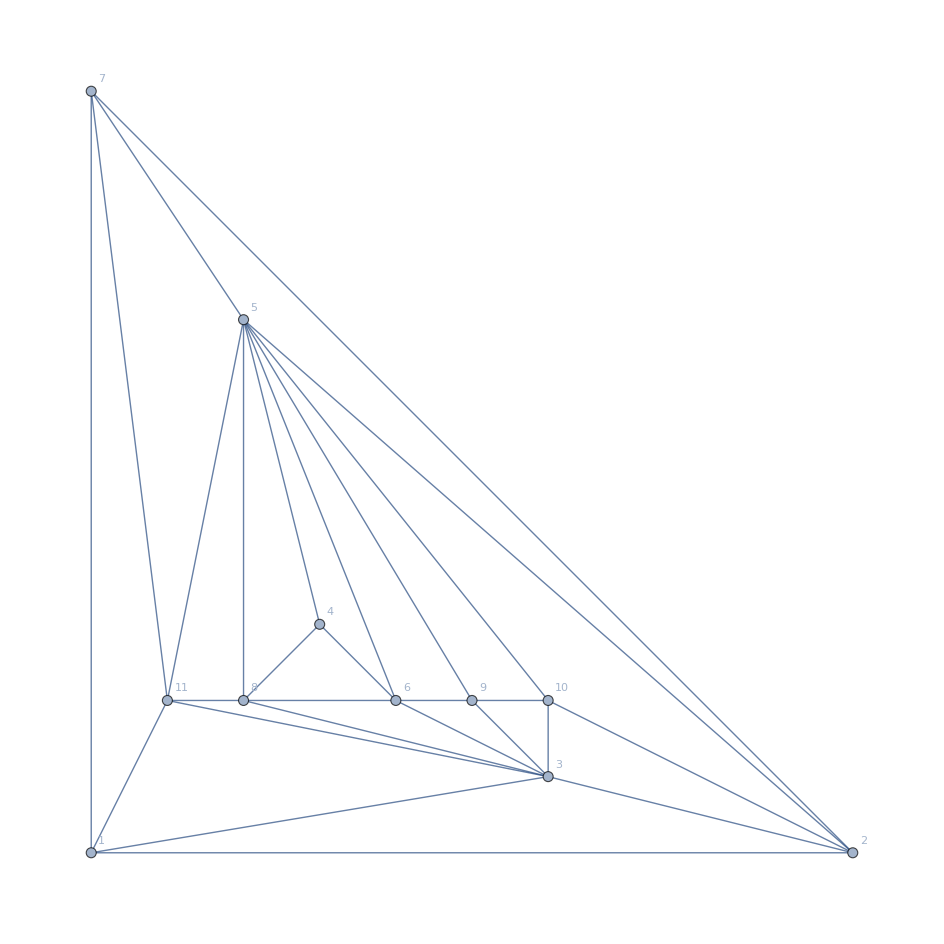

```mathematica
Graph[ReadGrof[500],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

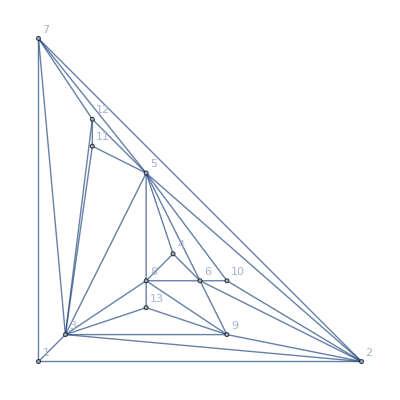
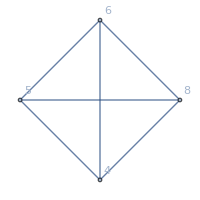
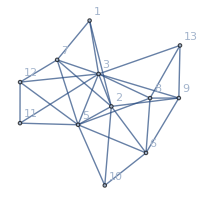
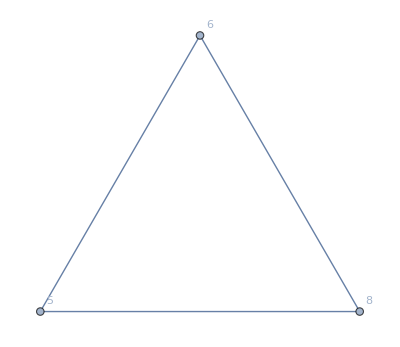
-Graphics-{(-3+x)^7 (-2+x) (-32+29 x-9 x^2+x^3),96,True}
v1x2x3 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96,True} | -Graphics-{-2+x,24,True}

```mathematica
ex2=WorkOnGraph[ReadGrof[50000],{5,6,8}]
```

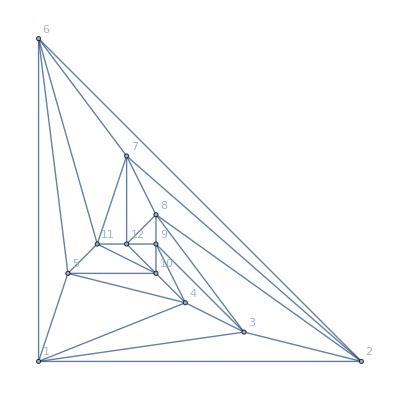

```mathematica
Graph[plantri[[1]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

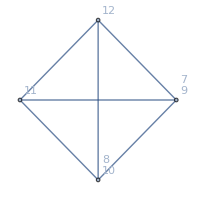
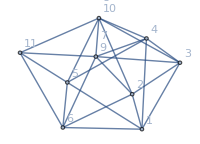
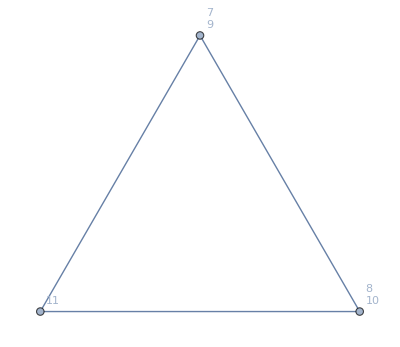
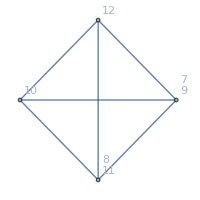
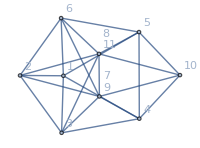
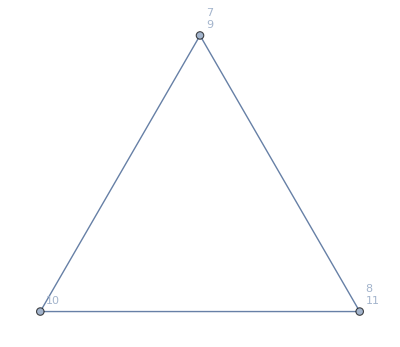
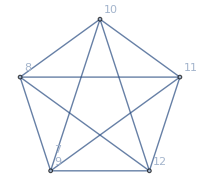
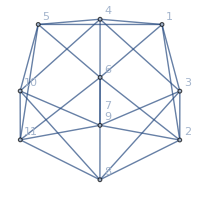
-Graphics-{(-3+x) (-2+x) (20170-40240 x+36408 x^2-19698 x^3+6999 x^4-1670 x^5+260 x^6-24 x^7+x^8),240,True}
-Graphics-361660 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48,False} | -Graphics-{-2+x,24,True}
-Graphics-361120 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48,False} | -Graphics-{-2+x,24,True}
-Graphics-360850 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-317380 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48,False} | -Graphics-{-2+x,24,True}
-Graphics-317140 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48,False} | -Graphics-{-2+x,24,True}
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-296080 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48,False} | -Graphics-{-2+x,24,True}
-Graphics-296050 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295510 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295270 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (3130-4282 x+2559 x^2-865 x^3+175 x^4-20 x^5+x^6),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}

```mathematica
WorkOnGraph[Graph[plantri[[1]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{7,8,9,10,11}]
```

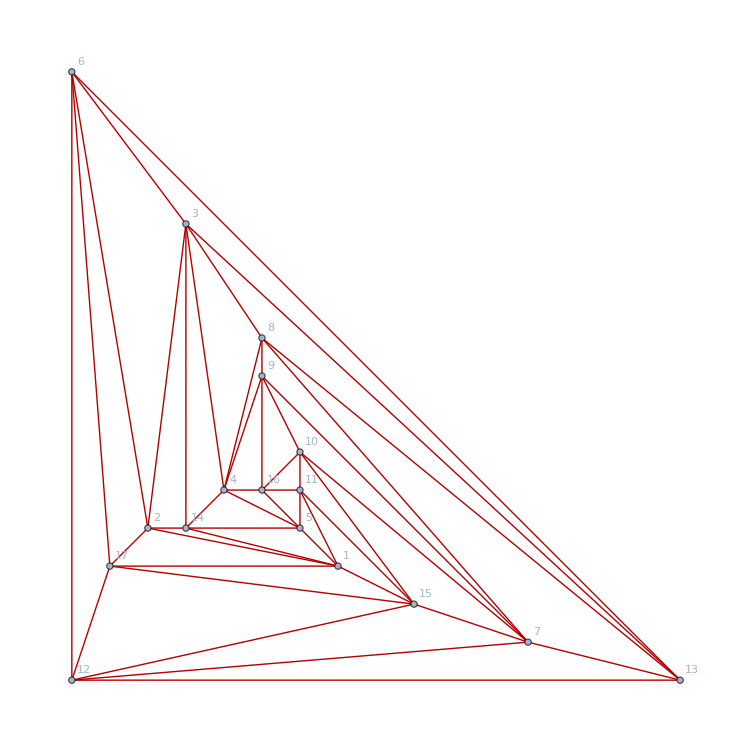

```mathematica
With[{g=Graph[plantri8,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]},Graph[g,GraphHighlight->CollectMPGEdges[g]]]
```

```mathematica
Select[VertexList[plantri8],VertexDegree[plantri8,#]==5&]
```

{12,13,17,6,8,9,10,11,2,14,16,5}

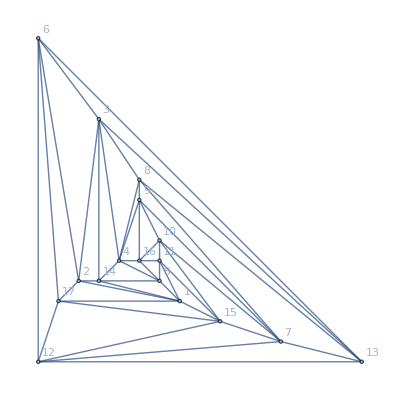
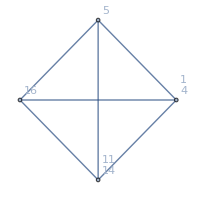
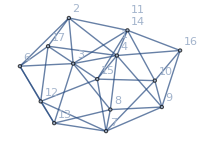
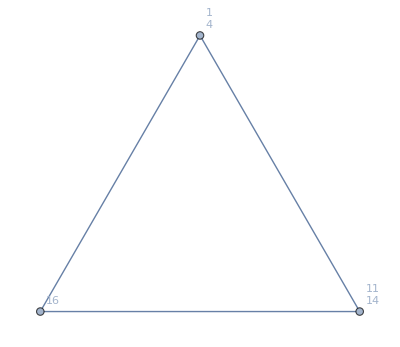
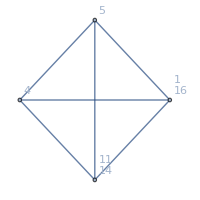
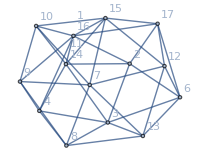
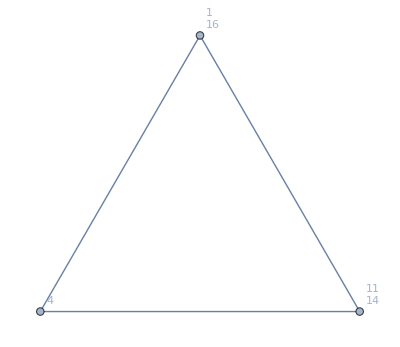
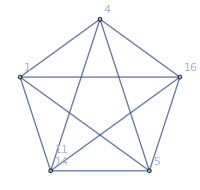
-Graphics-{(-3+x) (-2+x) (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13),528,True}
-Graphics-317380 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (431160-1030177 x+1135933 x^2-763950 x^3+347912 x^4-112261 x^5+25997 x^6-4263 x^7+473 x^8-32 x^9+x^10),96,False} | -Graphics-{-2+x,24,True}
-Graphics-361120 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (477266-1110564 x+1196204 x^2-789158 x^3+354267 x^4-113227 x^5+26079 x^6-4266 x^7+473 x^8-32 x^9+x^10),48,False} | -Graphics-{-2+x,24,True}
-Graphics-295510 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1697989+4334879 x-5168679 x^2+3814519 x^3-1941163 x^4+716005 x^5-195269 x^6+39318 x^7-5716 x^8+570 x^9-35 x^10+x^11),168,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-361660 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (420479-1004543 x+1107776 x^2-745914 x^3+340668 x^4-110411 x^5+25705 x^6-4237 x^7+472 x^8-32 x^9+x^10),72,False} | -Graphics-{-2+x,24,True}
-Graphics-296080 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (464246-1086280 x+1176371 x^2-779942 x^3+351634 x^4-112765 x^5+26033 x^6-4264 x^7+473 x^8-32 x^9+x^10),144,False} | -Graphics-{-2+x,24,True}
-Graphics-296050 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1527628+3960029 x-4797374 x^2+3596359 x^3-1857122 x^4+693958 x^5-191331 x^6+38857 x^7-5684 x^8+569 x^9-35 x^10+x^11),192,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-317140 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (439375-1044042 x+1145834 x^2-767775 x^3+348754 x^4-112361 x^5+26002 x^6-4263 x^7+473 x^8-32 x^9+x^10),168,False} | -Graphics-{-2+x,24,True}
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),216,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-360850 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1591333+4095711 x-4924725 x^2+3665216 x^3-1880588 x^4+699119 x^5-192046 x^6+38914 x^7-5686 x^8+569 x^9-35 x^10+x^11),168,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295270 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1722634+4384689 x-5212247 x^2+3835895 x^3-1947514 x^4+717147 x^5-195384 x^6+39323 x^7-5716 x^8+570 x^9-35 x^10+x^11),240,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (-1857524+4621632 x-5394228 x^2+3916057 x^3-1969792 x^4+721176 x^5-195851 x^6+39355 x^7-5717 x^8+570 x^9-35 x^10+x^11),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}

```mathematica
WorkOnGraph[Graph[plantri8,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{1,11,16,4,14}]
```

```mathematica
WorkOnGraph[Graph[plantri8,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{1,2,3,4,16,5}]
```

-Graphics-{(-3+x) (-2+x) (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13),528,True}
v135x24x6 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-94331+214415 x-222148 x^2+137758 x^3-56369 x^4+15788 x^5-3027 x^6+383 x^7-29 x^8+x^9),24,False} | -Graphics-{-2+x,24,True}
v13x24x5x6 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (518446-1233991 x+1351415 x^2-899458 x^3+403849 x^4-128004 x^5+29022 x^6-4646 x^7+502 x^8-33 x^9+x^10),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
v13x25x4x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (507880-1214349 x+1335989 x^2-892768 x^3+402103 x^4-127727 x^5+28997 x^6-4645 x^7+502 x^8-33 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v135x26x4 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-99128+221039 x-225812 x^2+138775 x^3-56511 x^4+15796 x^5-3027 x^6+383 x^7-29 x^8+x^9),96,False} | -Graphics-{-2+x,24,True}
v13x26x4x5 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (545548-1275682 x+1378312 x^2-908800 x^3+405697 x^4-128202 x^5+29031 x^6-4646 x^7+502 x^8-33 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v135x2x4x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (319189-795916 x+921110 x^2-650792 x^3+310358 x^4-104202 x^5+24903 x^6-4177 x^7+470 x^8-32 x^9+x^10),120,False} | -Graphics-{(-3+x) (-2+x),24,True}
v13x2x4x5x6 | -Graphics-{(-4+x)^2 (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (570021-1312172 x+1402113 x^2-917692 x^3+407771 x^4-128506 x^5+29057 x^6-4647 x^7+502 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v14x26x35 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-162025+339551 x-324601 x^2+186504 x^3-71183 x^4+18747 x^5-3408 x^6+412 x^7-30 x^8+x^9),72,False} | -Graphics-{-2+x,24,True}
v14x2x35x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (507880-1214349 x+1335989 x^2-892768 x^3+402103 x^4-127727 x^5+28997 x^6-4645 x^7+502 x^8-33 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x24x35x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (532034-1259808 x+1372848 x^2-909511 x^3+406717 x^4-128500 x^5+29070 x^6-4648 x^7+502 x^8-33 x^9+x^10),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x26x35x4 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (561804-1304318 x+1400911 x^2-919090 x^3+408589 x^4-128699 x^5+29079 x^6-4648 x^7+502 x^8-33 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x2x35x4x6 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (583609-1337989 x+1423546 x^2-927745 x^3+410639 x^4-129002 x^5+29105 x^6-4649 x^7+502 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v14x25x36 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (-180987+370383 x-346380 x^2+195198 x^3-73307 x^4+19065 x^5-3435 x^6+413 x^7-30 x^8+x^9),24,False} | -Graphics-{-2+x,24,True}
v14x2x36x5 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (605102-1389959 x+1475647 x^2-956898 x^3+420787 x^4-131281 x^5+29430 x^6-4676 x^7+503 x^8-33 x^9+x^10),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
v15x24x36 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-4+x) (-3+x) (-2+x) (32430-60637 x+51521 x^2-26133 x^3+8690 x^4-1943 x^5+285 x^6-25 x^7+x^8),0,False} | -Graphics-{-2+x,24,True}
v15x2x36x4 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (425356-1012994 x+1115392 x^2-750250 x^3+342225 x^4-110748 x^5+25745 x^6-4239 x^7+472 x^8-32 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x24x36x5 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-4+x) (-3+x) (-2+x) (-157314+319526 x-298245 x^2+168849 x^3-64138 x^4+16979 x^5-3131 x^6+387 x^7-29 x^8+x^9),0,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x25x36x4 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (618690-1415776 x+1497080 x^2-966951 x^3+423655 x^4-131777 x^5+29478 x^6-4678 x^7+503 x^8-33 x^9+x^10),48,False} | -Graphics-{(-3+x) (-2+x),24,True}
v1x2x36x4x5 | -Graphics-{(-4+x)^2 (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (680831-1513599 x+1563204 x^2-991875 x^3+429323 x^4-132556 x^5+29538 x^6-4680 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v14x25x3x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (570777-1332861 x+1434778 x^2-940497 x^3+416775 x^4-130678 x^5+29378 x^6-4674 x^7+503 x^8-33 x^9+x^10),120,False} | -Graphics-{(-3+x) (-2+x),24,True}
v14x26x3x5 | -Graphics-{(-3+x)^2 (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (608445-1394194 x+1477101 x^2-956529 x^3+420369 x^4-131153 x^5+29412 x^6-4675 x^7+503 x^8-33 x^9+x^10),120,False} | -Graphics-{(-3+x) (-2+x),24,True}
v14x2x3x5x6 | -Graphics-{(-4+x)^2 (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (632918-1430684 x+1500902 x^2-965421 x^3+422443 x^4-131457 x^5+29438 x^6-4676 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v15x24x3x6 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (416976-995379 x+1100396 x^2-743403 x^3+340388 x^4-110455 x^5+25719 x^6-4238 x^7+472 x^8-32 x^9+x^10),96,False} | -Graphics-{(-3+x) (-2+x),24,True}
v15x26x3x4 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (428699-1017229 x+1116846 x^2-749881 x^3+341807 x^4-110620 x^5+25727 x^6-4238 x^7+472 x^8-32 x^9+x^10),168,False} | -Graphics-{(-3+x) (-2+x),24,True}
v15x2x3x4x6 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (453172-1053719 x+1140647 x^2-758773 x^3+343881 x^4-110924 x^5+25753 x^6-4239 x^7+472 x^8-32 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v1x24x3x5x6 | -Graphics-{(-4+x)^2 (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (657072-1476143 x+1537761 x^2-982164 x^3+427057 x^4-132230 x^5+29511 x^6-4679 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v1x25x3x4x6 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (646506-1456501 x+1522335 x^2-975474 x^3+425311 x^4-131953 x^5+29486 x^6-4678 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v1x26x3x4x5 | -Graphics-{(-4+x)^2 (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (684174-1517834 x+1564658 x^2-991506 x^3+428905 x^4-132428 x^5+29520 x^6-4679 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}
v1x2x3x4x5x6 | -Graphics-{(-5+x)^2 (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x) (708647-1554324 x+1588459 x^2-1000398 x^3+430979 x^4-132732 x^5+29546 x^6-4680 x^7+503 x^8-33 x^9+x^10),0,False} | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False}

```mathematica
WorkOnGraph[Graph[plantri8,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{1,2,3,4,5}]
```

-Graphics-{(-3+x) (-2+x) (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13),528,True}
-Graphics-361660 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),72,False} | -Graphics-{-2+x,24,True}
-Graphics-361120 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),192,False} | -Graphics-{-2+x,24,True}
-Graphics-360850 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),216,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-317140 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (424115-1019576 x+1129267 x^2-761700 x^3+347480 x^4-112216 x^5+25995 x^6-4263 x^7+473 x^8-32 x^9+x^10),72,False} | -Graphics-{-2+x,24,True}
-Graphics-296080 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-4+x) (-3+x) (-2+x) (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9),0,False} | -Graphics-{-2+x,24,True}
-Graphics-295270 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),144,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-317380 | -Graphics-{(-3+x) (-2+x),24,True} | -Graphics-{(-3+x) (-2+x) (446420-1054643 x+1152500 x^2-770025 x^3+349186 x^4-112406 x^5+26004 x^6-4263 x^7+473 x^8-32 x^9+x^10),192,False} | -Graphics-{-2+x,24,True}
-Graphics-317110 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1453015+3808444 x-4663525 x^2+3529321 x^3-1836315 x^4+689866 x^5-190834 x^6+38823 x^7-5683 x^8+569 x^9-35 x^10+x^11),216,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-296050 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1679278+4306457 x-5153943 x^2+3813503 x^3-1943287 x^4+717022 x^5-195485 x^6+39341 x^7-5717 x^8+570 x^9-35 x^10+x^11),144,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295510 | -Graphics-{(-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-3+x) (-2+x) (-1746193+4433963 x-5258709 x^2+3861711 x^3-1956730 x^4+719298 x^5-195702 x^6+39350 x^7-5717 x^8+570 x^9-35 x^10+x^11),264,False} | -Graphics-{(-3+x) (-2+x),24,True}
-Graphics-295240 | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x) (-1859948+4632058 x-5410091 x^2+3928457 x^3-1975462 x^4+722760 x^5-196118 x^6+39380 x^7-5718 x^8+570 x^9-35 x^10+x^11),0,False} | -Graphics-{(-4+x) (-3+x) (-2+x),0,False}